Saddlenode bifurcation at x=0;  The diverging arrows/streamlines are suggestive that x=0 is an unstable saddle node. This is a saddlenode bifurcation example.

{{x→-√μ},{x→√μ}}

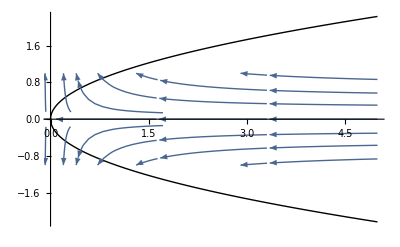

```mathematica
Clear[x,xdot,μ,y];
xdot=μ-x^2;
Solve[xdot==0,x]
μ=0.;
Plot[{μ-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,0,5},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ-x^2,y},{x,-5,5},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
μ=0.;
StreamPlot[{μ-x^2,y},{x,-5,5},{y,-1,1},GridLines->Automatic];
```

Two equilibrium equations exist: x=0 and x=μ.  When μ<0, the equilibrium is stable (streamlines move towards the equilibrium point).  When μ>0, the equilbrium is unstable (streamlines diverge or move away from the equilibrium point).  When μ=0, the equilibrium is unstable (the streamlines still move away from the equilibrium point, x=0).  This is known as a transcritical bifurcation at the parameter value, μ=0.  There is an “Exchange of stability” at μ=0.

{{x→0},{x→μ}}

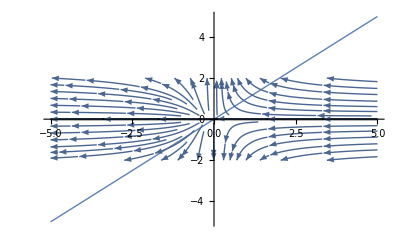

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^2;
Solve[xdot==0,x]
μ=0.;
Plot[{μ x-x^2},{x,-1,1},PlotStyle->{Thick,Black}];
Show[Plot[{μ,0},{μ,-5,5},PlotStyle->{Thick,Black}],
StreamPlot[{μ x-x^2,y},{x,-5,5},{y,-2,2},GridLines->Automatic,StreamScale->Medium]
]
```

Three equilibrium points exist at x=0, Sqrt[μ] and -Sqrt[μ].  Only at μ=0 is this equilibrium point stable (streamlines converge towards the equilibrium point).  At μ>0 and μ<0, the equilibrium point is unstable (streamlines diverge away from this point).

{{x→0},{x→-√μ},{x→√μ}}

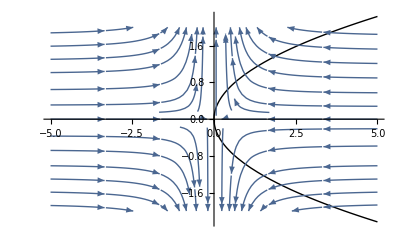

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^3;
Solve[xdot==0,x]
μ=0;
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-5,5},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,y},{x,-5,5},{y,-2,2},GridLines->Automatic,StreamScale->Medium]
]
```

The Lienhard equaton (which can be modified to the Van der Pol oscillator) is used next.  The phase portrait and the streamplot at μ=-0.3 suggest a stable focal point (streamlines converge into the focal point).  For a μ=1.0, the focal point is unstable (streamlines diverge away from the focal point).  The focal point, in this case is the origin.  This is an example of the Hopf bifurcation.

InterpolatingFunction[{{0., 80.}}, <>]

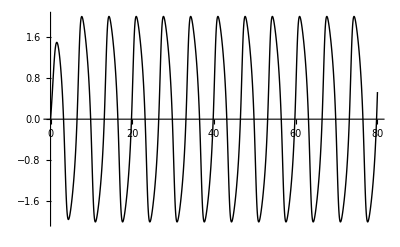

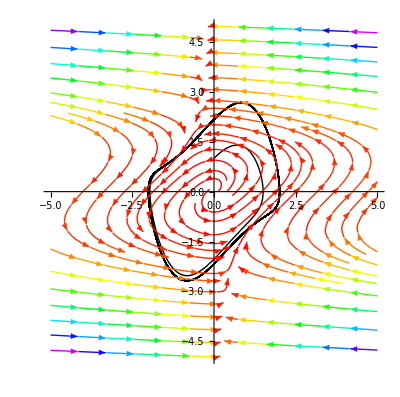

```mathematica
Clear[μ,s,x,t,tmax];
μ=1;tmax=80;
s=NDSolveValue[{x''[t]-(μ-x[t]^2)x'[t]+x[t]==0,x[0]==0,x'[0]==1},x,{t,0,tmax}]
Plot[s[t],{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All]
Show[
ParametricPlot[{s[t],s'[t]},{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All],
StreamPlot[{-u+(μ-u^2)v,v},{v,-5,5},{u,-5,5},StreamColorFunction->Hue,StreamPoints->40]
]
```

The Van der Pol oscillator is next used.  For a “highly nonlinear” problem (ϵ=0.99), the vdp oscillator describes an unstable focal point.  For a “weakly nonlinear” problem with (ϵ=0.1), the focal point is stable.  This is a Hopf bifurcation example, again.

InterpolatingFunction[{{0., 10.}}, <>]

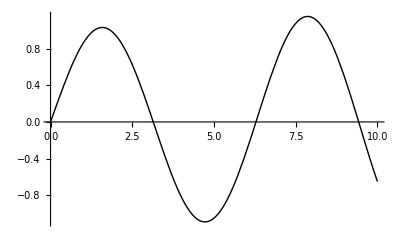

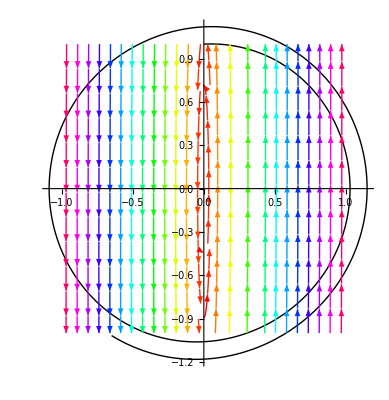

```mathematica
Clear[μ,s,x,t,tmax];
ϵ=0.05;tmax=10;
s=NDSolveValue[{x''[t]-ϵ(1-x[t]^2)x'[t]+x[t]==0,x[0]==0,x'[0]==1},x,{t,0,tmax}]
Plot[s[t],{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All]
Show[
ParametricPlot[{s[t],s'[t]},{t,0,tmax},PlotStyle->{Thick,Black},PlotRange->All],
StreamPlot[{ϵ (x-(x^3/3)-y),x/ϵ},{x,-1,1},{y,-1,1},StreamColorFunction->Hue,StreamPoints->40]
]
```

Steven Strogatz examples

{{x→0},{x→0},{x→0}}

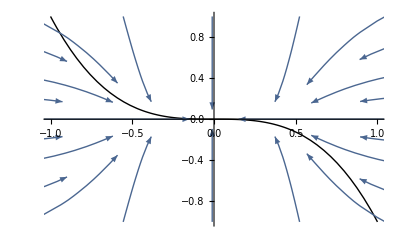

```mathematica
Clear[x,xdot,μ,y];
xdot=-x^3;
Solve[xdot==0,x]
Plot[{-x^3},{x,-1,1}];
Show[Plot[{-x^3},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{-x^3,-y},{x,-5,5},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

{{x→0},{x→0},{x→0}}

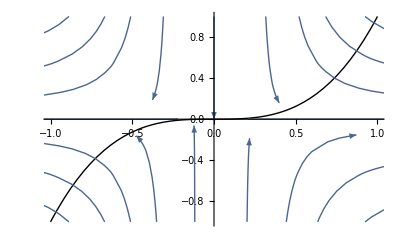

```mathematica
Clear[x,xdot,μ,y];
xdot=x^3;
Solve[xdot==0,x]
Plot[{x^3},{x,-1,1}];
Show[Plot[{x^3},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{x^3,-y},{x,-5,5},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

{{x→0},{x→0}}

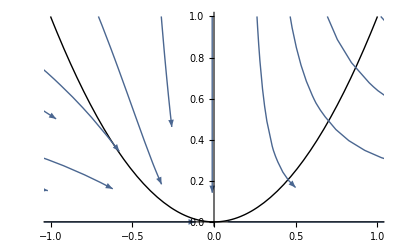

```mathematica
Clear[x,xdot,μ,y];
xdot=x^2;
Solve[xdot==0,x]
Plot[{x^2},{x,-1,1}];
Show[Plot[{x^2},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{x^2,-y},{x,-5,5},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

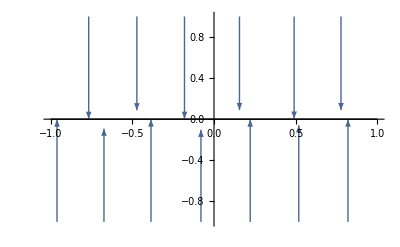

```mathematica
Clear[x,xdot,μ,y];
xdot=0;
Plot[{0},{x,-1,1}];
Show[Plot[{0},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{0,-y},{x,-5,5},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

{{x→0}}

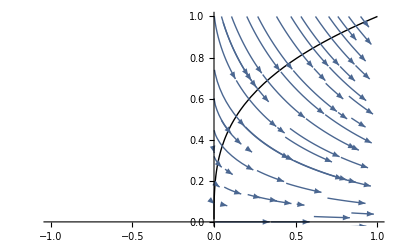

```mathematica
Clear[x,xdot,μ,y];
xdot=x^(1/3);
Solve[xdot==0,x]
Show[Plot[{x^(1/3)},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{x^(1/3),-y},{x,-1,1},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

{{x→-ⅈ},{x→ⅈ}}

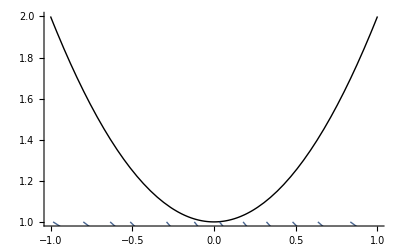

```mathematica
Clear[x,xdot,μ,y];
xdot=1+x^2;
Solve[xdot==0,x]
Show[Plot[{xdot},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{xdot,-y},{x,-1,1},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

Graphing of potentials: Steven Strogatz

x^2/2

{{x→0}}

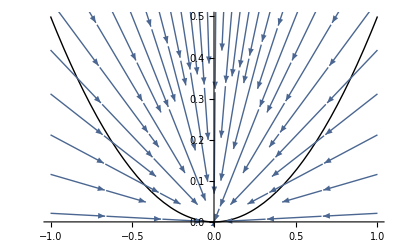

```mathematica
Clear[x,xdot,μ,y];
xdot=-x;
V=-Integrate[xdot,x]
Solve[xdot==0,x]
Show[Plot[{V},{x,-1,1},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{xdot,-y},{x,-1,1},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

Below (xdot=x-x^3) creates a “double well potential” which is bistable.

-x^2/2+x^4/4

{{x→-1},{x→0},{x→1}}

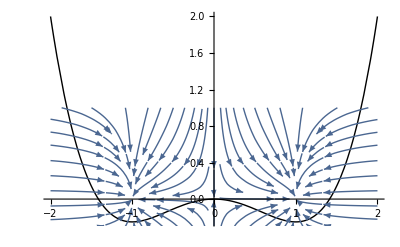

```mathematica
Clear[x,xdot,μ,y];
xdot=x-x^3;
V=-Integrate[xdot,x]
Solve[xdot==0,x]
Show[Plot[{V},{x,-2,2},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{xdot,-y},{x,-2,2},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```

Logistic equation with r=1, K=1 (Strogatz 2.8.1)

-x^2/2+x^3/3

{x→0,x→1}

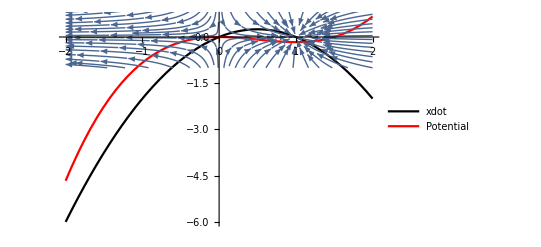

{0,0}

{0,-1/6}

```mathematica
Clear[x,xdot,μ,y];
xdot=x(1-x);
V=-Integrate[xdot,x]
roots=Solve[xdot==0,x]//Flatten
Show[Plot[{xdot,V},{x,-2,2},PlotStyle->{{Thick,Black},{Thick,Red}},PlotLegends->{"xdot","Potential"}],
StreamPlot[{xdot,-y},{x,-2,2},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
{xdot/.x->roots[[1]][[2]],xdot/.x->roots[[2]][[2]]}
{V/.x->roots[[1]][[2]],V/.x->roots[[2]][[2]]}
```

Strogatz Chapter 3.  xdot=r+x^2.The potential reveals that the vector roll down the potential hill towards the trough which is the stable point (stationary point).  For r<0, there exists a stable point.  For r=0, there exists a “delicate” stable point which disappears as soon as r>0 (the vectors keep rolling away from the previously stable point).  Plotting r vs x is the bifurcation plot (finding roots of xdot and plotting them against r).

-r x-x^3/3

{x→-ⅈ √r,x→ⅈ √r}

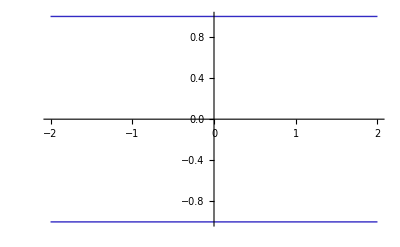

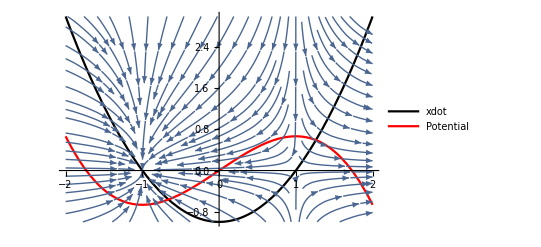

```mathematica
Clear[x,xdot,r,rval,V,y];
xdot=r+x^2;
V=-Integrate[xdot,x]
roots=Solve[xdot==0,x]//Flatten
rval=-1.;
Plot[{roots[[1]][[2]]/.r->rval,roots[[2]][[2]]/.r->rval},{x,-2,2},PlotStyle->{{Thick,RGBColor[0.2,0.17,0.77]}}]
Show[
Plot[{xdot/.r->rval,V/.r->rval},{x,-2,2},PlotStyle->{{Thick,Black},{Thick,Red}},PlotLegends->{"xdot","Potential"}],
StreamPlot[{xdot/.r->rval,-y},{x,-2,2},{y,-1,3},GridLines->Automatic,StreamScale->Medium]
]
```

Pitchfork bifurcation and its potential

-(r x^2)/2+x^4/4

{x→0,x→-√r,x→√r}

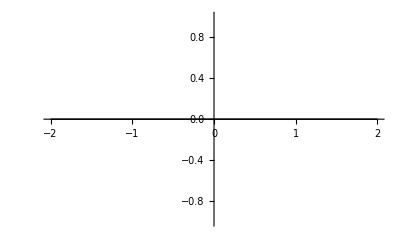

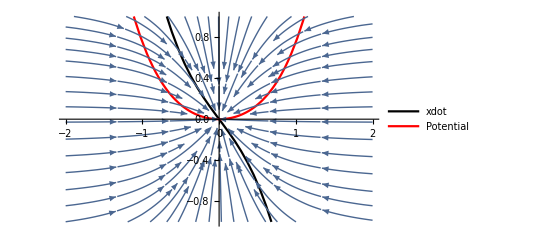

```mathematica
Clear[x,xdot,r,rval,V,y];
xdot=r x-x^3;
V=-Integrate[xdot,x]
roots=Solve[xdot==0,x]//Flatten
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]]},{x,-2,2},PlotStyle->{{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{-2,2},{-1,1}}]
rval=-1.;
Show[
Plot[{xdot/.r->rval,V/.r->rval},{x,-2,2},PlotStyle->{{Thick,Black},{Thick,Red}},PlotLegends->{"xdot","Potential"},PlotRange->{{-2,2},{-1,1}}],
StreamPlot[{xdot/.r->rval,-y},{x,-2,2},{y,-1,1},GridLines->Automatic,StreamScale->Medium]
]
```